```mathematica
Quit[];
```

```mathematica
(*HEALTHY state*)
Wss=0;
Wgs=1.12;
Wsg=19;
Wgg=6.6;
Wcs=2.42;
Wxg=15.1;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS= 6 (*tau_s=tau_g*);
```

```mathematica
(*coefficients and function in rescaled system*)
Wgs=.;
Wsg=.;
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_,Wgs_,Wsg_]:={
-u[[1]]+f1[tu+ac*ud[[1]]-Wgs*ud[[2]]],
-u[[2]]+f2[tv+Wsg*ud[[1]]+dc*ud[[2]]]}
eq[Wgs_,Wsg_]:={u,v}/.FindRoot[F[{u,v},{u,v},Wgs,Wsg]=={0,0},{{u,0},{v,0}}]
alpha[Wgs_,Wsg_]:=ac*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]+dc*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
beta[Wgs_,Wsg_]:=(ac*dc+Wgs*Wsg)*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
```

```mathematica
(*computation of critical tau for Hopf bifurcation, according to Theorem 2.8*)
rho[w_]:=1;
theta[w_]:=w;
mu[Wgs_,Wsg_]:=If[Length[NSolve[beta[Wgs,Wsg]==x*(alpha[Wgs,Wsg]-x)&&x<-1,x]]≥1,x/.NSolve[beta[Wgs,Wsg]==x*(alpha[Wgs,Wsg]-x)&&x<-1,x][[1]],0
];
w[Wgs_,Wsg_]:=If[mu[Wgs,Wsg]==0,
x/.FindRoot[rho[x]*alpha[Wgs,Wsg]==2*(Cos[theta[x]]-Sqrt[beta[Wgs,Wsg]*rho[x]^2-1]*Sin[theta[x]]),{x,Pi/2,0,Pi}],
x/.FindRoot[rho[x]*Cos[theta[x]]==1/mu[Wgs,Wsg],{x,Pi/2,0,Pi}]];
tau[Wgs_,Wsg_]:=If[mu[Wgs,Wsg]==0,
w[Wgs,Wsg]/Sqrt[beta[Wgs,Wsg]*rho[w[Wgs,Wsg]]^2-1],-w[Wgs,Wsg]*Cot[w[Wgs,Wsg]]]
```

```mathematica
(*healthy parameter values*)
Wgs=1.12;
Wsg=19;
mu[Wgs,Wsg]
w[Wgs,Wsg]
tau[Wgs,Wsg]
```

-1.85722

2.13938

1.367

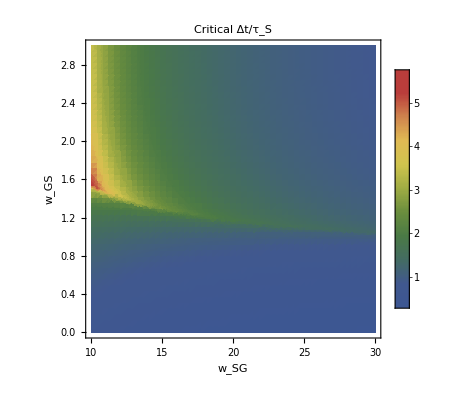

```mathematica
(*around healthy state parameters*)
DensityPlot[tau[Wgs,Wsg],{Wsg,10,30},{Wgs,0,3},PlotLegends->Automatic,PlotPoints->50,ColorFunction->"DarkRainbow",PlotRange->{0,10},FrameLabel->{"w_SG","w_GS"},MeshFunctions->{#3&},Mesh->{{1,2,3,4,5}},PlotLabel->"Critical Δt/τ_S"]
```

```mathematica
Quit[];
```

```mathematica
(*DISEASED state*)
Wss=0;
Wgs=10.7;
Wsg=20;
Wgg=12.3;
Wcs=9.2;
Wxg=139.4;
Ctx=27;
Str=2;
Ms = 300;
Mg = 400;
Bs = 17;
Bg = 75;
tauS=6 (*tau_s=tau_g*);
```

```mathematica
(*coefficients and function in rescaled system*)
Wgs=.;
Wsg=.;
ac=Wss;
bc=-Wgs;
cc=Wsg;
dc=-Wgg;
tu=Wcs*Ctx;
tv=-Wxg*Str;
f1[in1_]:=Ms/(1+Exp[-4*in1/Ms]*(Ms-Bs)/Bs);
f2[in2_]:=Mg/(1+Exp[-4*in2/Mg]*(Mg-Bg)/Bg);
F[u_,ud_,Wgs_,Wsg_]:={
-u[[1]]+f1[tu+ac*ud[[1]]-Wgs*ud[[2]]],
-u[[2]]+f2[tv+Wsg*ud[[1]]+dc*ud[[2]]]}
eq[Wgs_,Wsg_]:={u,v}/.FindRoot[F[{u,v},{u,v},Wgs,Wsg]=={0,0},{{u,0},{v,0}}]
alpha[Wgs_,Wsg_]:=ac*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]+dc*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
beta[Wgs_,Wsg_]:=(ac*dc+Wgs*Wsg)*f1'[tu+ac*eq[Wgs,Wsg][[1]]-Wgs*eq[Wgs,Wsg][[2]]]*f2'[tv+Wsg*eq[Wgs,Wsg][[1]]+dc*eq[Wgs,Wsg][[2]]]
```

```mathematica
(*computation of critical tau for Hopf bifurcation, according to Theorem 2.8*)
rho[w_]:=1;
theta[w_]:=w;
mu[Wgs_,Wsg_]:=If[Length[NSolve[beta[Wgs,Wsg]==x*(alpha[Wgs,Wsg]-x)&&x<-1,x]]≥1,x/.NSolve[beta[Wgs,Wsg]==x*(alpha[Wgs,Wsg]-x)&&x<-1,x][[1]],0
];
w[Wgs_,Wsg_]:=If[mu[Wgs,Wsg]==0,
x/.FindRoot[rho[x]*alpha[Wgs,Wsg]==2*(Cos[theta[x]]-Sqrt[beta[Wgs,Wsg]*rho[x]^2-1]*Sin[theta[x]]),{x,Pi/2,0,Pi}],
x/.FindRoot[rho[x]*Cos[theta[x]]==1/mu[Wgs,Wsg],{x,Pi/2,0,Pi}]];
tau[Wgs_,Wsg_]:=If[mu[Wgs,Wsg]==0,
w[Wgs,Wsg]/Sqrt[beta[Wgs,Wsg]*rho[w[Wgs,Wsg]]^2-1],-w[Wgs,Wsg]*Cot[w[Wgs,Wsg]]]
```

```mathematica
(*diseased*)
Wgs=10.7;
Wsg=20;
mu[Wgs,Wsg]
w[Wgs,Wsg]
tau[Wgs,Wsg]
```

0

0.69188

0.216411

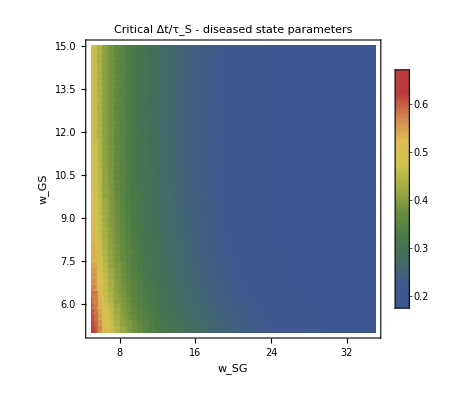

```mathematica
(*around diseased state parameters*)
DensityPlot[tau[Wgs,Wsg],{Wsg,5,35},{Wgs,5,15},PlotLegends->Automatic,PlotPoints->50,ColorFunction->"DarkRainbow",PlotRange->{0,1},FrameLabel->{"w_SG","w_GS"},MeshFunctions->{#3&},Mesh->{{0.2,0.3,0.4,0.5,0.6}},PlotLabel->"Critical Δt/τ_S - diseased state parameters"]
```